# Quantum chaos in quantum walks

## Configuration

```mathematica
SeedRandom[67];
```

```mathematica
(* Size of matrices *)
size=1000;
```

## Content

### Generating the matrices

We’ll generate a random matrices following both a GOE and a Poisson distribution

```mathematica
(goe=RandomVariate[GaussianOrthogonalMatrixDistribution[size]])//MatrixForm
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

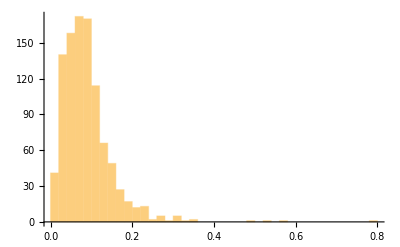

```mathematica
Histogram[Eigenvalues[goe]//Sort//Differences,"PDF"]
```

```mathematica
(poisson=RandomVariate[PoissonDistribution[10],{size,size}])//MatrixForm (* 9 *)
```